```mathematica
SetDirectory["S:\\文档0\\Ex Machina Project File\\PRJ_MMAVideo\\EP3"]
```

S:\文档0\Ex Machina Project File\PRJ_MMAVideo\EP3

```mathematica
session=StartWebSession[]
```

WebSessionObject[…]

```mathematica
DeleteObject[session]
```

```mathematica
aid=820260320;
data=URLExecute[{"https://api.bilibili.com/x/v2/reply/main"},{"jsonp"->"jsonp","next"->0,"type"->"1","oid"->ToString[aid],"sort"->"2"}];
pos=Position[data,"message"];
tpos=Table[Delete[pos[[m]],-1],{m,1,Length[pos]}];
replyA=Delete[Extract[data,tpos],1][[;;4]]
```

{message→有人喜欢抖音，也有人对乔伊向真理和自由献身表示赞赏，二者都是喜欢。
但是，对抖音低创的喜欢，是发自真心的，还是因为生活所迫亦或是辨别鉴赏能力不足（例如小孩），没有时间去欣赏如乔伊一样的创作者呢？
一幅画作、一部电影、一本小说，乃至游戏，我们去玩他们的时候，若是仅仅为了短暂的欢愉来麻痹自己的话，与一台没有灵魂的机器无异，这么做仅仅是为了“上油”而已，今朝上油明日亦是，只是浑浑噩噩度日。
但是，我们若是能看到很多的超越认识的好作品时，哪怕一个瞬间这些作品引起了思考，为什么我会觉得这部作品好，乔伊介绍过很多优秀的游戏，也许去亲自体验一番过后，给自己一点时间来反思，为什么这款游戏似乎比我曾经见过的更好？然后得出答案，但答案未必是正确的，当见到下一款超越审美认知的游戏，这份答案会再一次修订，一次又一次，这就是审美的提高，或者说，我们对人类刻在DNA里的认知变得更加了解了。
譬如说我们写作文，老师教我们要欲扬先抑，为什么这样会是“好的”？通俗来说，齐氏效应，读者带入主人公，故事在给主人公压力，而释放压力的时候，读者会感到畅快，这就是为什么要这么做。
游戏也是一样的，但绝大部分开发者并不理解这一层，所以我们看到了不计其数的、亮点乏善可陈的“复制品”，杀塔也好、吸血鬼幸存者也好、类魂也好。
我是一名玩家，然后才是鉴赏家、批评家，最后才是策划，我经历过被克金游戏坑蒙拐骗，我经历过提笔忘字的难熬写稿，而现在我只有一个很简单的目标，让更多的玩家理解审美，提高审美，而这任重道远。,message→可是，为了生活还在上油的人们并不能看完你所说的的,message→回复 @一只可爱却又无害的猹 :任重道远。,message→怎么说呢，整个项目从一开始就没有做好项目规划，这个品类玩家群体有多少，自己要做到什么要的程度，需要多少开发成本，能够卖多少份。如果国产独立游戏都是这样的情况，做的时候爽就完事了，投资人会更不看好独立游戏，也对不起工作室手下的员工。}

```mathematica
reply={};
aid=820260320;
max=90;
ProgressIndicator[Dynamic[index],{1,max}]
Table[
data=URLExecute[{"https://api.bilibili.com/x/v2/reply/main"},{"jsonp"->"jsonp","next"->ToString[page],"type"->"1","oid"->ToString[aid],"sort"->"2"}];
Pause[RandomReal[{.5,1.5}]];
pos=Position[data,"message"];
tpos=Table[Delete[pos[[m]],-1],{m,1,Length[pos]}];
replyA=Delete[Extract[data,tpos],1];
index=page;
reply=Join[reply,Table["message"/.replyA[[n]],{n,1,Length[replyA]}]];
,{page,1,max}];
Dimensions[reply]
```

{1194}

```mathematica
fix=DeleteDuplicates[StringReplace[{"["~~__~~"]","回复 @"~~__~~":","@"~~__~~" ","●"}->""]/@reply];
```

```mathematica
fix=StringReplace[{"["~~__~~"]","回复 @"~~__~~":","@"~~__~~" ","●"}->""]/@reply;
```

```mathematica
Length[%108]
```

106

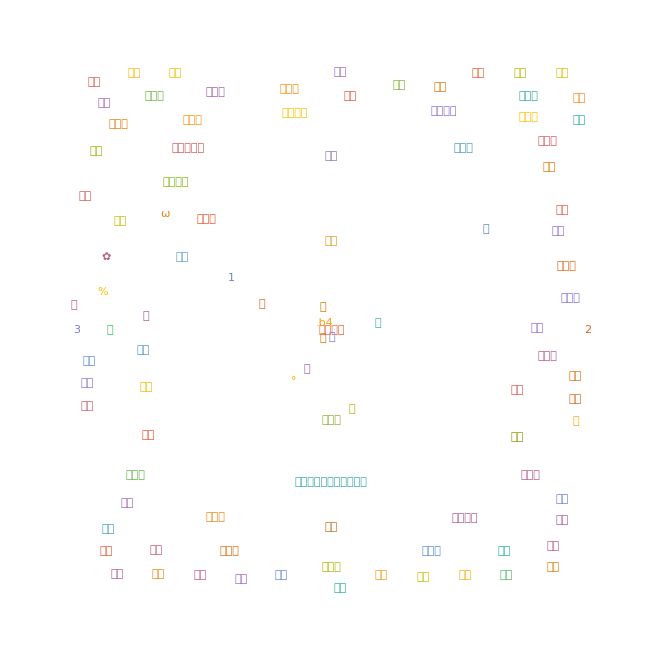

```mathematica
pic=WordCloud[WordCounts[ToString[fix]]]
```

```mathematica
Export["H_2_reply.png",Rasterize[pic,Background->None,ImageResolution->500]]
```

H_2_reply.png

```mathematica
a0=WebExecute[session,"LocateElements"->"CSSSelector"->"#folder0 > div.opened > div:nth-child(4) > span:nth-child(2)"]
f0=WebExecute[session,"ElementText"->a0]
```

{WebElementObject[…]}

{3088}

```mathematica
a0=WebExecute[session,"LocateElements"->"CSSSelector"->"#folder0 > div.opened > div:nth-child(4) > span:nth-child(2)"];
f0=ToExpression@If[FailureQ[WebExecute[session,"ElementText"->a0]],"",WebExecute[session,"ElementText"->a0]][[1]];
Print["Total objects to analyse is ",f0-7];
ProgressIndicator[Dynamic[index],{0,f0}]
f={};
tab=Table[a=WebExecute[session,"LocateElements"->"CSSSelector"->"#folder0 > div.opened > div:nth-child("<>ToString[n]<>") > span:nth-child(2)"];
f=Join[f,If[FailureQ[WebExecute[session,"ElementText"->a]],"",WebExecute[session,"ElementText"->a]]];
index=n;
,{n,8,f0}];
Dimensions[f]
```

Total objects to analyse is 3081

{3081}

```mathematica
Head@fix
```

Symbol

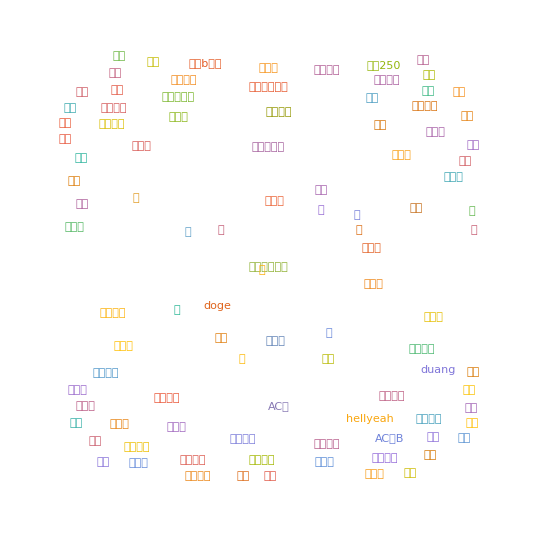

```mathematica
data=Table[StringReplace[ToString[f[[n]]],{Whitespace->"", "哈哈哈哈" .. -> "哈哈哈哈"}],{n,1,Length[f]}];
wcd=WordCounts[ToString[data]];
WordCloud[wcd]
```

```mathematica
Export["",Rasterize[pic,Background->None,ImageResolution->500]]
```

```mathematica
Streams
```

```mathematica
str=OpenRead["C:\Users\asus\Downloads\888131871.xml"]
```

InputStream[…]

```mathematica
Read[str, Word]
```

p="626.06700,1,25,16777215,1673692190,0,ecb94f4,1229778245734429952,0">å¤.aaå.bc.baä.ba.86</d><d

```mathematica
$CharacterEncoding="ISOLatin1"
```

ISOLatin1

```mathematica
Import["C:\\Users\\asus\\Downloads\\888131871.xml",CharacterEncoding->"ISOLatin1"]
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Encoding→UTF-8]},XMLElement[i,{},{XMLElement[chatserver,{},{chat.bilibili.com}],XMLElement[chatid,{},{888131871}],XMLElement[mission,{},{0}],3090,XMLElement[d,{p→17.06900,1,25,16777215,1668272446,0,c6368740,1184314131180692992,0},{熟悉的AC部}],XMLElement[d,{p→0.55100,1,25,16777215,1668272420,0,1ae96996,1184313916684003584,0},{耶！！！！}]}],{}]
 |  |  |  |

```mathematica
raw=URLExecute["https://www.tasteatlas.com/best"];
```

```mathematica
Head[raw]
```

String

```mathematica
"("~~Except[")"]..~~")"
```

```mathematica
StringReplace[raw,Whitespace->" "]
```

World's Best Dishes World's Best Cuisines World's Best Local Restaurants AWARDS 2022 Best Traditional Food in the World BD Best Traditional Dishes in the World 100 best rated dishes in the world in 2022. 1 Stew Karē 4.92 Japan Best in Soup Curry & Dining Suage (Sapporo, Japan) 2 Meat Cut Picanha 4.86 Brazil Best in Casa da Picanha Penedo (Penedo, Brazil) 3 Clam Dish Amêijoas à Bulhão Pato 4.86 Portugal Best in A Marisqueira de Matosinhos (Porto, Portugal) 4 Dumplings Tangbao 4.83 China Best in Din Tai Fung Shanghai (Shanghai, China) 5 Dumplings Guotie 4.81 China Best in Xindalu China Kitchen (Shanghai, China) 6 Stew Phanaeng Curry 4.80 Thailand Best in Kopitiam By Wilai (Phuket, Thailand) 7 Seafood Ceviche mixto 4.79 Peru Best in La Mar Cebichería (Miraflores, Peru) 8 Stew Ghormeh sabzi 4.79 Iran Best in Moslem Restaurant (Tehran, Iran) 9 Lamb/Mutton Dish Cağ kebabı 4.78 Turkiye Best in Şehzade Cağ Kebap (Fatih, Turkiye) 10 Chicken Dish Pollo a la brasa 4.74 Peru Best in Tinajas Chicken & Grill (San Borja, Peru) 11 Pizza Pizza Margherita 4.71 Italy Best in Pizzeria Starita a Materdei (Naples, Italy) 12 Dumplings Xiaolongbao 4.71 China Best in Din Tai Fung Shanghai (Shanghai, China) 13 Shrimp/Prawn Dish Gambas al ajillo 4.70 Spain Best in El Bálamu (Llanes, Spain) 14 Meat Dish Shish kebab 4.70 Turkiye Best in Paşa Kebap (Fethiye, Turkiye) 15 Lamb/Mutton Dish Païdakia 4.69 Greece Best in To Steki Tou Ilia (Athens, Greece) 16 Dumplings Pierogi Ruskie 4.68 Poland Best in Pod Baranem (Kraków, Poland) 17 Pork Dish Cochinita pibil 4.68 Mexico Best in Taqueria Honorio (Tulum, Mexico) 18 Dumplings Cha siu bao 4.68 China Best in Mott 32 (Hong Kong, China) 19 Pasta Pappardelle al cinghiale 4.68 Italy Best in Trattoria Sergio Gozzi (Florence, Italy) 20 Pork Dish Carnitas 4.67 Mexico Best in Taqueria Chabelo (Mexico City, Mexico) 21 Noodle Dish Tonkotsu ramen 4.67 Japan Best in Ichiran Dotonbori (Osaka, Japan) 22 Dumplings Manti 4.67 Turkiye Best in Bodrum Manti & Cafe (Beşiktaş, Turkiye) 23 Cheese Dish Raclette 4.67 Switzerland Best in Auberge de Saviese (Geneva, Switzerland) 24 Pasta Trofie al pesto 4.67 Italy Best in Gastronomia San Martino (Monterosso al Mare, Italy) 25 Pork Dish Carne de porco à Alentejana 4.67 Portugal Best in Tasca do Celso (Vila Nova de Milfontes, Portugal) 26 Duck Dish Pečená kachna 4.67 Czech Republic Best in U Kroka (Prague, Czech Republic) 27 Shrimp/Prawn Dish Gambas à la plancha 4.66 Spain Best in Bar Goiz-Argi (San Sebastián, Spain) 28 Stew Shahi paneer 4.66 India Best in Kake Da Hotel (New Delhi, India) 29 Beef Dish Vaca atolada 4.65 Brazil Best in Casinha Mineira (São Paulo, Brazil) 30 Rice Dish Katsudon 4.64 Japan Best in Katsudon Hozenji Yokocho (Osaka, Japan) 31 Meat Dish Gyros 4.63 Greece Best in Pitogyros (Oia, Greece) 32 Beef Dish Steak au poivre 4.63 France Best in Au Terminus du Châtelet (Paris, France) 33 Pasta Linguine allo scoglio 4.63 Italy Best in Bagni Delfino (Sorrento, Italy) 34 Chicken Dish Frango assado com piri piri 4.63 Portugal Best in Restaurante O Teodósio (Guia, Portugal) 35 Chicken Dish Inasal na manok 4.63 Philippines Best in Balay Dako (Tagaytay, Philippines) 36 Casserole Giouvetsi 4.62 Greece Best in Lithos Tavern (Athens, Greece) 37 Pork Dish Pernil 4.62 Puerto Rico Best in Deaverdura (San Juan, United States of America) 38 Pizza Prosciutto e funghi pizza 4.62 Italy Best in Angelo Pezzella - Pizzeria con cucina (Rome, Italy) 39 Lamb/Mutton Dish İskender kebap 4.61 Turkiye Best in Yesil Izgara Pideli Kofte (Bursa, Turkiye) 40 Stew Massaman Curry 4.61 Thailand Best in Issaya Siamese Club (Bangkok, Thailand) 41 Saltwater Fish Dish Bakaliaros 4.60 Greece Best in Damigos (Athens, Greece) 42 Pasta Tagliatelle al ragù alla Bolognese 4.59 Italy Best in Trattoria di Via Serra (Bologna, Italy) 43 Stew Karē raisu 4.59 Japan Best in Rojiura Curry Samurai Shimokitazawa (Setagaya, Japan) 44 Noodle Dish Shoyu ramen 4.59 Japan Best in Matsu Shokudou (Kitakata, Japan) 45 Lamb/Mutton Dish Alinazik Kebab 4.59 Turkiye Best in İmam Çağdaş Kebap ve Baklava Salonu (Gaziantep, Turkiye) 46 Rice Dish Sake nigiri sushi 4.59 Japan Best in Sushi Dai (Chūō, Japan) 47 Dumplings Gyoza 4.58 Japan Best in Chao Chao Sanjo Kiyamachi (Kyoto, Japan) 48 Meat Dish Döner kebab 4.57 Turkiye Best in Bayramoğlu Döner (Beykoz, Turkiye) 49 Stew Moqueca 4.57 Brazil Best in Coco Bambu JK (São Paulo, Brazil) 50 Meat Dish Feijão tropeiro 4.57 Brazil Best in Virada's do Largo (Tiradentes, Brazil) 51 Offal Dish Kokoretsi 4.57 Greece Best in Ziogas (Athens, Greece) 52 Fish Dish Tiradito 4.57 Peru Best in Astrid y Gaston (San Isidro, Peru) 53 Chicken Dish Butter Chicken 4.56 India Best in Gulati (New Delhi, India) 54 Noodle Dish Yaki-udon 4.56 Japan Best in Darumado (Kitakyushu, Japan) 55 Stew Korma 4.55 India Best in Dastarkhwan (Lucknow, India) 56 Shrimp/Prawn Dish Ebi furai 4.55 Japan Best in Katsukura Tonkatsu (Kyoto, Japan) 57 Pasta Pasta carbonara 4.54 Italy Best in Cantina e Cucina (Rome, Italy) 58 Savory Pie Khachapuri 4.54 Georgia Best in Funicular Complex (Tbilisi, Georgia) 59 Meat Dish Souvlaki 4.54 Greece Best in To Araliki (Kavala, Greece) 60 Meat Cut Bistecca alla Fiorentina 4.54 Italy Best in Trattoria Sergio Gozzi (Florence, Italy) 61 Vegetable Dish Yemista 4.54 Greece Best in Kouzina EPE (Chania City, Greece) 62 Pork Dish Sisig 4.54 Philippines Best in Locavore (Pasig, Philippines) 63 Dumplings Shuǐjiǎo 4.54 China Best in Mr. Shi's Dumplings (Dongcheng District, China) 64 Ground Meat Dish Ćevapi 4.53 Bosnia and Herzegovina Best in Ćevabdžinica Tima-Irma (Mostar, Bosnia and Herzegovina) 65 Stew Pozole 4.53 Mexico Best in La Chata (Guadalajara, Mexico) 66 Pork Dish Kotlet schabowy 4.53 Poland Best in Smakolyki Restaurant (Kraków, Poland) 67 Beef Dish Gyūdon 4.53 Japan Best in Matsuya (Shibuya, Japan) 68 Meat Dish Anticucho 4.53 Peru Best in Panchita (Miraflores, Peru) 69 Noodle Dish Dan Dan Noodles 4.53 China Best in Noodle & Congee Corner Restaurant (Macau, China) 70 Dumplings Gnocchi alla Sorrentina 4.53 Italy Best in Mangia (Catania, Italy) 71 Pork Dish Vindaloo 4.53 India Best in Venite (Panaji, India) 72 Beef Dish Milanesa napolitana 4.53 Argentina Best in La Fonda Del Tío (Bariloche, Argentina) 73 Stew Green Curry 4.52 Thailand Best in Benjarong (Bangkok, Thailand) 74 Wrap Tantuni 4.52 Turkiye Best in Suat Usta 33 Mersin Tantuni (Beyoğlu, Turkiye) 75 Stew Hünkar beğendi 4.52 Turkiye Best in Karaköy Lokantası (Beyoğlu, Turkiye) 76 Pasta Lasagne alla Bolognese 4.51 Italy Best in Sfoglia Rina (Bologna, Italy) 77 Pizza Pizza quattro formaggi 4.51 Italy Best in I Masanielli di Francesco Martucci (Caserta, Italy) 78 Rice Dish Tteokbokki 4.51 South Korea Best in Apple House (Seoul, South Korea) 79 Rice Dish Hyderabadi biryani 4.51 India Best in ITC Kohenur (Hyderabad, India) 80 Lamb/Mutton Dish Çöp şiş 4.51 Turkiye Best in Kalyon Lazutti (Ortaklar, Turkiye) 81 Lamb/Mutton Dish Adana kebap 4.50 Turkiye Best in Beyzade Kebap (Adana, Turkiye) 82 Duck Dish Peking Duck 4.50 China Best in Jingzun Peking Duck Restaurant (Chaoyang District, China) 83 Noodle Dish Miso ramen 4.50 Japan Best in Ramen Oyaji Machida (Machida, Japan) 84 Pizza Pizza alla diavola 4.50 Italy Best in Gusta Pizza (Florence, Italy) 85 Noodle Dish Shio ramen 4.50 Japan Best in Ramen Sen no Kaze (Kyoto, Japan) 86 Beef Dish Svíčková 4.50 Czech Republic Best in U Kroka (Prague, Czech Republic) 87 Stew Stifado 4.50 Greece Best in Taverna Alekos (Rethymno City, Greece) 88 Chicken Dish Aji de gallina 4.50 Peru Best in Panchita (Miraflores, Peru) 89 Pork Dish Leitão da bairrada 4.50 Portugal Best in Pedro dos Leitões (Mealhada, Portugal) 90 Dumplings Khinkali 4.49 Georgia Best in Amo Rame (Tbilisi, Georgia) 91 Rice Dish Uramaki 4.49 United States of America Best in Sushi Ota (San Diego, United States of America) 92 Ground Meat Dish Sarma 4.48 Turkiye Best in Hayvore (Beyoğlu, Turkiye) 93 Pasta Cacio e pepe 4.48 Italy Best in Pastasciutta (Rome, Italy) 94 Pizza Pizza ai funghi 4.48 Italy Best in Sisini La Casa del Suppli (Rome, Italy) 95 Pork Dish Porchetta 4.48 Italy Best in Macelleria Peppe Cotto (Loro Piceno, Italy) 96 Rice Dish Arroz chaufa 4.48 Peru Best in Chifa Internacional (Miraflores, Peru) 97 Ground Meat Dish Sheftalia 4.48 Cyprus Best in Letymbou Tavern (Paphos, Cyprus) 98 Squid Dish Kalamarakia tiganita 4.47 Greece Best in Thalassino Ageri (Chania City, Greece) 99 Ground Meat Dish Pljeskavica 4.47 Serbia Best in Toster Bar (Novi Sad, Serbia) 100 Dumplings Shumai 4.47 China Best in One Harbour Road (Hong Kong, China) Show All World's Best Dishes World's Best Cuisines World's Best Local Restaurants The best traditional food and legendary restaurants you have to try in 2023 © 2023 by TasteAtlas Awards | Terms of Use | Privacy Policy

```mathematica
StringSplit[StringReplace[raw,Whitespace->" "]][[35;;]]
```

{1,Stew,Karē,4.92,Japan,Best,in,Soup,Curry,&,Dining,Suage,(Sapporo,,Japan),2,Meat,Cut,Picanha,4.86,Brazil,Best,in,Casa,da,Picanha,Penedo,(Penedo,,Brazil),3,Clam,Dish,Amêijoas,à,Bulhão,Pato,4.86,Portugal,Best,in,A,Marisqueira,de,Matosinhos,(Porto,,Portugal),4,Dumplings,Tangbao,4.83,China,Best,in,Din,Tai,Fung,Shanghai,(Shanghai,,China),5,Dumplings,Guotie,4.81,China,Best,in,Xindalu,China,Kitchen,(Shanghai,,China),6,Stew,Phanaeng,Curry,4.80,Thailand,Best,in,Kopitiam,By,Wilai,(Phuket,,Thailand),7,Seafood,Ceviche,mixto,4.79,Peru,Best,in,La,Mar,Cebichería,(Miraflores,,Peru),8,Stew,Ghormeh,sabzi,4.79,Iran,Best,in,Moslem,Restaurant,(Tehran,,Iran),9,Lamb/Mutton,Dish,Cağ,kebabı,4.78,Turkiye,Best,in,Şehzade,Cağ,Kebap,(Fatih,,Turkiye),10,Chicken,Dish,Pollo,a,la,brasa,4.74,Peru,Best,in,Tinajas,Chicken,&,Grill,(San,Borja,,Peru),11,Pizza,Pizza,Margherita,4.71,Italy,Best,in,Pizzeria,Starita,a,Materdei,(Naples,,Italy),12,Dumplings,Xiaolongbao,4.71,China,Best,in,Din,Tai,Fung,Shanghai,(Shanghai,,China),13,Shrimp/Prawn,Dish,Gambas,al,ajillo,4.70,Spain,Best,in,El,Bálamu,(Llanes,,Spain),14,Meat,Dish,Shish,kebab,4.70,Turkiye,Best,in,Paşa,Kebap,(Fethiye,,Turkiye),15,Lamb/Mutton,Dish,Païdakia,4.69,Greece,Best,in,To,Steki,Tou,Ilia,(Athens,,Greece),16,Dumplings,Pierogi,Ruskie,4.68,Poland,Best,in,Pod,Baranem,(Kraków,,Poland),17,Pork,Dish,Cochinita,pibil,4.68,Mexico,Best,in,Taqueria,Honorio,(Tulum,,Mexico),18,Dumplings,Cha,siu,bao,4.68,China,Best,in,Mott,32,(Hong,Kong,,China),19,Pasta,Pappardelle,al,cinghiale,4.68,Italy,Best,in,Trattoria,Sergio,Gozzi,(Florence,,Italy),20,Pork,Dish,Carnitas,4.67,Mexico,Best,in,Taqueria,Chabelo,(Mexico,City,,Mexico),21,Noodle,Dish,Tonkotsu,ramen,4.67,Japan,Best,in,Ichiran,Dotonbori,(Osaka,,Japan),22,Dumplings,Manti,4.67,Turkiye,Best,in,Bodrum,Manti,&,Cafe,(Beşiktaş,,Turkiye),23,Cheese,Dish,Raclette,4.67,Switzerland,Best,in,Auberge,de,Saviese,(Geneva,,Switzerland),24,Pasta,Trofie,al,pesto,4.67,Italy,Best,in,Gastronomia,San,Martino,(Monterosso,al,Mare,,Italy),25,Pork,Dish,Carne,de,porco,à,Alentejana,4.67,Portugal,Best,in,Tasca,do,Celso,(Vila,Nova,de,Milfontes,,Portugal),26,Duck,Dish,Pečená,kachna,4.67,Czech,Republic,Best,in,U,Kroka,(Prague,,Czech,Republic),27,Shrimp/Prawn,Dish,Gambas,à,la,plancha,4.66,Spain,Best,in,Bar,Goiz-Argi,(San,Sebastián,,Spain),28,Stew,Shahi,paneer,4.66,India,Best,in,Kake,Da,Hotel,(New,Delhi,,India),29,Beef,Dish,Vaca,atolada,4.65,Brazil,Best,in,Casinha,Mineira,(São,Paulo,,Brazil),30,Rice,Dish,Katsudon,4.64,Japan,Best,in,Katsudon,Hozenji,Yokocho,(Osaka,,Japan),31,Meat,Dish,Gyros,4.63,Greece,Best,in,Pitogyros,(Oia,,Greece),32,Beef,Dish,Steak,au,poivre,4.63,France,Best,in,Au,Terminus,du,Châtelet,(Paris,,France),33,Pasta,Linguine,allo,scoglio,4.63,Italy,Best,in,Bagni,Delfino,(Sorrento,,Italy),34,Chicken,Dish,Frango,assado,com,piri,piri,4.63,Portugal,Best,in,Restaurante,O,Teodósio,(Guia,,Portugal),35,Chicken,Dish,Inasal,na,manok,4.63,Philippines,Best,in,Balay,Dako,(Tagaytay,,Philippines),36,Casserole,Giouvetsi,4.62,Greece,Best,in,Lithos,Tavern,(Athens,,Greece),37,Pork,Dish,Pernil,4.62,Puerto,Rico,Best,in,Deaverdura,(San,Juan,,United,States,of,America),38,Pizza,Prosciutto,e,funghi,pizza,4.62,Italy,Best,in,Angelo,Pezzella,-,Pizzeria,con,cucina,(Rome,,Italy),39,Lamb/Mutton,Dish,İskender,kebap,4.61,Turkiye,Best,in,Yesil,Izgara,Pideli,Kofte,(Bursa,,Turkiye),40,Stew,Massaman,Curry,4.61,Thailand,Best,in,Issaya,Siamese,Club,(Bangkok,,Thailand),41,Saltwater,Fish,Dish,Bakaliaros,4.60,Greece,Best,in,Damigos,(Athens,,Greece),42,Pasta,Tagliatelle,al,ragù,alla,Bolognese,4.59,Italy,Best,in,Trattoria,di,Via,Serra,(Bologna,,Italy),43,Stew,Karē,raisu,4.59,Japan,Best,in,Rojiura,Curry,Samurai,Shimokitazawa,(Setagaya,,Japan),44,Noodle,Dish,Shoyu,ramen,4.59,Japan,Best,in,Matsu,Shokudou,(Kitakata,,Japan),45,Lamb/Mutton,Dish,Alinazik,Kebab,4.59,Turkiye,Best,in,İmam,Çağdaş,Kebap,ve,Baklava,Salonu,(Gaziantep,,Turkiye),46,Rice,Dish,Sake,nigiri,sushi,4.59,Japan,Best,in,Sushi,Dai,(Chūō,,Japan),47,Dumplings,Gyoza,4.58,Japan,Best,in,Chao,Chao,Sanjo,Kiyamachi,(Kyoto,,Japan),48,Meat,Dish,Döner,kebab,4.57,Turkiye,Best,in,Bayramoğlu,Döner,(Beykoz,,Turkiye),49,Stew,Moqueca,4.57,Brazil,Best,in,Coco,Bambu,JK,(São,Paulo,,Brazil),50,Meat,Dish,Feijão,tropeiro,4.57,Brazil,Best,in,Virada's,do,Largo,(Tiradentes,,Brazil),51,Offal,Dish,Kokoretsi,4.57,Greece,Best,in,Ziogas,(Athens,,Greece),52,Fish,Dish,Tiradito,4.57,Peru,Best,in,Astrid,y,Gaston,(San,Isidro,,Peru),53,Chicken,Dish,Butter,Chicken,4.56,India,Best,in,Gulati,(New,Delhi,,India),54,Noodle,Dish,Yaki-udon,4.56,Japan,Best,in,Darumado,(Kitakyushu,,Japan),55,Stew,Korma,4.55,India,Best,in,Dastarkhwan,(Lucknow,,India),56,Shrimp/Prawn,Dish,Ebi,furai,4.55,Japan,Best,in,Katsukura,Tonkatsu,(Kyoto,,Japan),57,Pasta,Pasta,carbonara,4.54,Italy,Best,in,Cantina,e,Cucina,(Rome,,Italy),58,Savory,Pie,Khachapuri,4.54,Georgia,Best,in,Funicular,Complex,(Tbilisi,,Georgia),59,Meat,Dish,Souvlaki,4.54,Greece,Best,in,To,Araliki,(Kavala,,Greece),60,Meat,Cut,Bistecca,alla,Fiorentina,4.54,Italy,Best,in,Trattoria,Sergio,Gozzi,(Florence,,Italy),61,Vegetable,Dish,Yemista,4.54,Greece,Best,in,Kouzina,EPE,(Chania,City,,Greece),62,Pork,Dish,Sisig,4.54,Philippines,Best,in,Locavore,(Pasig,,Philippines),63,Dumplings,Shuǐjiǎo,4.54,China,Best,in,Mr.,Shi's,Dumplings,(Dongcheng,District,,China),64,Ground,Meat,Dish,Ćevapi,4.53,Bosnia,and,Herzegovina,Best,in,Ćevabdžinica,Tima-Irma,(Mostar,,Bosnia,and,Herzegovina),65,Stew,Pozole,4.53,Mexico,Best,in,La,Chata,(Guadalajara,,Mexico),66,Pork,Dish,Kotlet,schabowy,4.53,Poland,Best,in,Smakolyki,Restaurant,(Kraków,,Poland),67,Beef,Dish,Gyūdon,4.53,Japan,Best,in,Matsuya,(Shibuya,,Japan),68,Meat,Dish,Anticucho,4.53,Peru,Best,in,Panchita,(Miraflores,,Peru),69,Noodle,Dish,Dan,Dan,Noodles,4.53,China,Best,in,Noodle,&,Congee,Corner,Restaurant,(Macau,,China),70,Dumplings,Gnocchi,alla,Sorrentina,4.53,Italy,Best,in,Mangia,(Catania,,Italy),71,Pork,Dish,Vindaloo,4.53,India,Best,in,Venite,(Panaji,,India),72,Beef,Dish,Milanesa,napolitana,4.53,Argentina,Best,in,La,Fonda,Del,Tío,(Bariloche,,Argentina),73,Stew,Green,Curry,4.52,Thailand,Best,in,Benjarong,(Bangkok,,Thailand),74,Wrap,Tantuni,4.52,Turkiye,Best,in,Suat,Usta,33,Mersin,Tantuni,(Beyoğlu,,Turkiye),75,Stew,Hünkar,beğendi,4.52,Turkiye,Best,in,Karaköy,Lokantası,(Beyoğlu,,Turkiye),76,Pasta,Lasagne,alla,Bolognese,4.51,Italy,Best,in,Sfoglia,Rina,(Bologna,,Italy),77,Pizza,Pizza,quattro,formaggi,4.51,Italy,Best,in,I,Masanielli,di,Francesco,Martucci,(Caserta,,Italy),78,Rice,Dish,Tteokbokki,4.51,South,Korea,Best,in,Apple,House,(Seoul,,South,Korea),79,Rice,Dish,Hyderabadi,biryani,4.51,India,Best,in,ITC,Kohenur,(Hyderabad,,India),80,Lamb/Mutton,Dish,Çöp,şiş,4.51,Turkiye,Best,in,Kalyon,Lazutti,(Ortaklar,,Turkiye),81,Lamb/Mutton,Dish,Adana,kebap,4.50,Turkiye,Best,in,Beyzade,Kebap,(Adana,,Turkiye),82,Duck,Dish,Peking,Duck,4.50,China,Best,in,Jingzun,Peking,Duck,Restaurant,(Chaoyang,District,,China),83,Noodle,Dish,Miso,ramen,4.50,Japan,Best,in,Ramen,Oyaji,Machida,(Machida,,Japan),84,Pizza,Pizza,alla,diavola,4.50,Italy,Best,in,Gusta,Pizza,(Florence,,Italy),85,Noodle,Dish,Shio,ramen,4.50,Japan,Best,in,Ramen,Sen,no,Kaze,(Kyoto,,Japan),86,Beef,Dish,Svíčková,4.50,Czech,Republic,Best,in,U,Kroka,(Prague,,Czech,Republic),87,Stew,Stifado,4.50,Greece,Best,in,Taverna,Alekos,(Rethymno,City,,Greece),88,Chicken,Dish,Aji,de,gallina,4.50,Peru,Best,in,Panchita,(Miraflores,,Peru),89,Pork,Dish,Leitão,da,bairrada,4.50,Portugal,Best,in,Pedro,dos,Leitões,(Mealhada,,Portugal),90,Dumplings,Khinkali,4.49,Georgia,Best,in,Amo,Rame,(Tbilisi,,Georgia),91,Rice,Dish,Uramaki,4.49,United,States,of,America,Best,in,Sushi,Ota,(San,Diego,,United,States,of,America),92,Ground,Meat,Dish,Sarma,4.48,Turkiye,Best,in,Hayvore,(Beyoğlu,,Turkiye),93,Pasta,Cacio,e,pepe,4.48,Italy,Best,in,Pastasciutta,(Rome,,Italy),94,Pizza,Pizza,ai,funghi,4.48,Italy,Best,in,Sisini,La,Casa,del,Suppli,(Rome,,Italy),95,Pork,Dish,Porchetta,4.48,Italy,Best,in,Macelleria,Peppe,Cotto,(Loro,Piceno,,Italy),96,Rice,Dish,Arroz,chaufa,4.48,Peru,Best,in,Chifa,Internacional,(Miraflores,,Peru),97,Ground,Meat,Dish,Sheftalia,4.48,Cyprus,Best,in,Letymbou,Tavern,(Paphos,,Cyprus),98,Squid,Dish,Kalamarakia,tiganita,4.47,Greece,Best,in,Thalassino,Ageri,(Chania,City,,Greece),99,Ground,Meat,Dish,Pljeskavica,4.47,Serbia,Best,in,Toster,Bar,(Novi,Sad,,Serbia),100,Dumplings,Shumai,4.47,China,Best,in,One,Harbour,Road,(Hong,Kong,,China),Show,All,World's,Best,Dishes,World's,Best,Cuisines,World's,Best,Local,Restaurants,The,best,traditional,food,and,legendary,restaurants,you,have,to,try,in,2023,©,2023,by,TasteAtlas,Awards,|,Terms,of,Use,|,Privacy,Policy}